# Quantica

## Calculator of quantum systems with mathematica

20 December, 2013

## Sort technique

### 時間に依存しないHamiltonian

時間に依存しないハミルトニアンの固有値問題は

H|Φ_n⟩ = E_n|Φ_n⟩

であるので，求まったエネルギーE_n を小さい順に並べるnで|Φ_n⟩をsortすれば
nの昇順は基底状態から励起状態へ順に並ぶ．
QuanticaのEigenは標準でE_n小さい順に並び替えをする様に設計している．

```mathematica
Exit[]
```

```mathematica
Get["Quantica`"];
Quantica`MP`dps=20;
T[x_]:=x^2/2
V[x_]:=x^2/2
dim=40;
domain={{-2,2},{-2,2}};
QuanticaSetting[dim,domain,Verbose->True];
SetSystem[T,V];
Ham=FourierBase`Hamiltonian[];

{evals,evecs}=Eigen[Ham,Sort->False]; (*defalt Sort->True*)
Print[Re[evals][[1;;5]]/Hbar]
{evals,evecs}=Eigen[Ham]; (*defalt Sort->True*)
Print[Re[evals][[1;;5]]/Hbar]
```

{Dim:,40,Domain:,{{-2,2},{-2,2}},Tau:,1,dps:,20}

{54.94801341341901723,46.70079485432902441,43.79139280495104287,40.15832467163046608,38.22635540555889025}

{0.5,1.5,2.5,3.5,4.5}

### Kicked rotator

ユニタリー演算子の固有値問題の場合エネルギー固有値の分布が実数りからトーラス

E_n∈ℝ→𝕋=[0,2π)

に写されるのでエネルギ的な順序付けが意味をなさない．
しかしながら，HとUの対応を考えた方が見通しが良い場合があるので，Hに基づいてUの固有値を順序づけする．以下で示す例で順序に成功しない場合もあるので，case by caseで使い分けて欲しい

#### 固有状態に基づく順序付け

ユニタリー演算子の固有値問題を

U|ψ_m⟩ = E_n|ψ_m⟩

として

⟨ψ_m|Φ_n⟩ (n=0,1,2⋯)

が最大(最大で1)となるmを，m=nとして順序付けする．

```mathematica
?SortIndex
```

SortIndex[basis, evecs] <evecs_m|basos_n>が最大の値を返すmをn=0から順に求め，mのリストし返します

が実際に順序付けされたindexを返す．

```mathematica
Get["Quantica`"];
Quantica`MP`dps=20;
T[x_]:=x*x/2
V[x_]:=Cos[2*Pi*x]/(4*Pi*Pi)

dim=100;
domain={{0,1},{-1/2,1/2}};
QuanticaSetting[dim,domain,Verbose->True];
SetSystem[T,V];
Ham=FourierBase`Hamiltonian[];
{bchenergy,bchevecs}=Eigen[Ham];

U=Qmap`SymmetricUnitary[];
{uevals,uevecs}=Eigen[U];
sindex=SortIndex[bchevecs,uevecs];
{uevals,uevecs}=SortEigen[uevals,uevecs,sindex];
```

{Dim:,100,Domain:,{{0,1},{-1/2,1/2}},Tau:,1,dps:,20}

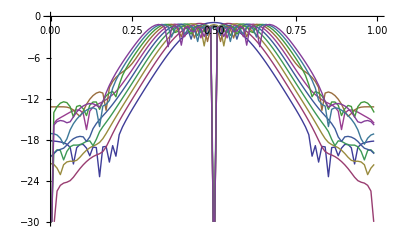

```mathematica
potential=Table[{X[[1]][[i]],V[X[[1]]][[i]]},{i,1,dim}];
data[n_] := Table[ { X[[1]][[i]],Log10[State`Abs2[ uevecs[[n]][[i]]]]},{i,1,dim}];
ListPlot[ Map[data,Range[10]],
Joined->True,PlotRange->{{0,1},{-30,0}}]
```